```mathematica
(*LandauTransition-HCC.nb
Bryan Daniels
2023.4.7
Making plots for the hepatocellular carcinoma example, using code from LandauTransition-PaperDataAnalysis.nb
*)
```

### Plot definitions

modified from LandauTransition-PaperDataAnalysis.nb

```mathematica
COLOR1=Lighter[Purple];
COLOR2=Orange;
```

```mathematica
bistablePlotEigvec[dataFullWithGroups_,fitMu_,fitVals_,fitVecs_,fitParams_,nuIndex_,runString_:""]:=
With[
{v=fitVecs[[nuIndex]],
transformedData=((#-fitMu-(nuMu/.fitParams[[nuIndex]][[2]]) fitVecs[[nuIndex]])&/@dataFullWithGroups[[2]]).fitVecs[[nuIndex]],
color1=COLOR1,
color2=COLOR2
},
Block[{colors,eigenvectorPlot},
colors=If[#=="control",color1,color2]&/@dataFullWithGroups[[1]];(*Blend[{{Min[transformedData],color1},{Max[transformedData],color2}},#]&/@transformedData;*)
(*Blend[{{-Max[Abs[transformedData]],color1},{Max[Abs[transformedData]],color2}},#]&/@transformedData*)
eigenvectorPlot=
Show[
bistableWellPlot[dataFullWithGroups[[2]],fitMu,fitVals,fitVecs,fitParams,nuIndex,fitVecs[[nuIndex]],colors](*,
Graphics[Rectangle[
{Min[transformedData],-2},
{Max[transformedData],-1}]]*)
];
Export["~/Dropbox (ASU)/Research/bees/geneExpression/Plots/"<>"230407_bistable_plot_along_eigvec_"<>runString<>"_nuIndex"<>ToString[nuIndex]<>".pdf",eigenvectorPlot]
]
]
```

```mathematica
(*make plot along single dimension*)
bistableWellPlot[dataFull_,fitMu_,fitVals_,fitVecs_,fitParams_,nuIndex_,projectionVec_,colors_(*,xmaxScale_:10*)]:=
With[
{c=c/.fitParams[[nuIndex]][[2]],
d=d/.fitParams[[nuIndex]][[2]],
nuMu=nuMu/.fitParams[[nuIndex]][[2]],
transformedData=((
#-fitMu
-(nuMu/.fitParams[[nuIndex]][[2]]) fitVecs[[nuIndex]]
)&/@dataFull).projectionVec},
Block[{scale,logymax,yscale,aratio},
aratio=1/5(*1/2*);
(*scale=(*2022/9/20 try fixed horizontal scale*)*)
scale=150(*0.8(Max[transformedData]-Min[transformedData])*)(*If[c<0,Sqrt[-xmaxScale c/d/fitVals[[nuIndex]]],Sqrt[xmaxScale c/fitVals[[nuIndex]]]]*);
yscale=2scale aratio ;
logymax=NMaxValue[{LandauTransitionDistributionLogPDFdiagonal[fitMu+nuMu fitVecs[[nuIndex]]+deltax projectionVec,fitMu,fitVals,fitVecs,nuIndex,c,d,nuMu],-scale<deltax<scale},deltax];
(*Print["logymax = ",logymax];*)
Show[
Plot[
yscale Exp[
(*LandauTransitionDistributionLogPDFdiagonal[fitMu,fitMu,fitVals,fitVecs,nuIndex,c,d]-*)LandauTransitionDistributionLogPDFdiagonal[fitMu+nuMu fitVecs[[nuIndex]]+deltax projectionVec,fitMu,fitVals,fitVecs,nuIndex,c,d,nuMu]-logymax
],
{deltax,-scale,scale},Filling->Bottom,Axes->{True,False},PlotRange->{0,1.075yscale}(*{-1.35,1.35}*)],
(*ListPlot[Transpose[{transformedData,ConstantArray[0,Length[dataFull]]}],
PlotStyle->PointSize[0.05]]*)
ScatterPlotColors[transformedData,
colors,
0.3 scale/10],
PlotRangeClipping->False,
AspectRatio->Automatic(*aratio*),
(*tick spacing*)
Ticks->{Range[-200,200,10Log[10]
(*Piecewise[{{0.5,scale<1},{Ceiling[scale/2],scale≥1}}]*)],Automatic},
(*remove tick labels*)TicksStyle->Directive[FontOpacity->0,FontSize->0]
]
]
]
```

```mathematica
(*new swarm plot version*)
(*previous version of below had radius=(Max[xList]-Min[xList])/40*)
ScatterPlotColors[xList_,colors_,radius_]:=beeswarmPlot[xList,colors,radius]
```

```mathematica
LandauTransitionDistributionRelativeLogPDF[x_,mu_,J_,nu_,c_,d_]:=-(1/2)(x-mu).J.(x-mu)-((c-1)/2)(nu.J.nu)((x-mu).nu)^2-(d/4)(nu.J.nu)^2((x-mu).nu)^4
```

```mathematica
(*for now we'll restrict nu to be along an eigenvector of J---the index of nu in Jvals is nuIndex*)logNormalizationDiagonal[Jvals_,nuIndex_,c_,d_]:=((Length[Jvals]-1)/2)Log[2π]+0.5(Log[Jvals[[nuIndex]]]-Plus@@Log[Jvals])+Log[If[c>0,(c ⅇ^(c^2/(8 d)) BesselK[1/4,c^2/(8 d)])/(√2 √(c d Jvals[[nuIndex]])),(ⅇ^(c^2/(8 d)) π (BesselI[-1/4,c^2/(8 d)]+BesselI[1/4,c^2/(8 d)]))/(2 √(-(d Jvals[[nuIndex]])/c))]]
```

```mathematica
(*(Assumes any zeros come at the end of Jvals for nuIndex to work)*)LandauTransitionDistributionLogPDFdiagonal[x_,mu_,Jvals_,Jvecs_,nuIndex_,c_,d_,nuMu_]:=
With[{
J=Transpose[Jvecs].DiagonalMatrix[Jvals].Jvecs,
nu=Jvecs[[nuIndex]]},
LandauTransitionDistributionRelativeLogPDF[x,mu+nuMu nu,J,nu,c,d]-logNormalizationDiagonal[Select[Jvals,#>0&],nuIndex,c,d]
]
```

#### bee swarm plot code (modified from https://mathematica.stackexchange.com/questions/42585/implementing-a-beeswarm-plot-in-mathematica )

```mathematica
intervalInverse[Interval[]]:=Interval[{-Infinity,Infinity}]
intervalInverse[Interval[int__]]:=Interval@@Partition[Replace[Flatten[{int}],{{-Infinity,mid___,Infinity}:>{mid},{-Infinity,mid__}:>{mid,Infinity},{mid__,Infinity}:>{-Infinity,mid},{mid___}:>{-Infinity,mid,Infinity}}],2]

intervalComplement[a_Interval,b__Interval]:=IntervalIntersection[a,intervalInverse@IntervalUnion[b]]
```

```mathematica
(*data is assumed to be a sorted vector of numbers*)beeswarm[data_,radius_]:=Module[{points,left,right,int},points={};
Do[int=Interval@@Cases[points,{x_,y_}/;y>pt-radius:>x+{-1,1} Sqrt[radius^2-(pt-y)^2]];
right=Min[intervalComplement[Interval[{0,Infinity}],int]];
left=Max[intervalComplement[Interval[{-Infinity,0}],int]];
AppendTo[points,{If[right<-left,right,right(*left*)],pt}],{pt,data}];
points]
```

```mathematica
beeswarmTwo[data_,diameter_]:=
Module[{filledRegion,points,yBest,radius,yinit},points={};radius=diameter/2;
Do[
filledRegion=If[Length[points]>0,RegionUnion[Disk[#,radius]&/@points],Disk[{-10radius,pt-10radius},radius/10]];
yinit=If[
Length[points]>0,
Max[points[[;;,1]]]+3radius,
0];
yBest=y/.Last[
FindMinimum[{y,{y>0,RegionDistance[filledRegion,{y,pt}]>=radius}},{y,yinit},AccuracyGoal->1,PrecisionGoal->1]];
AppendTo[points,{yBest,pt}],
{pt,data}];
points]
```

```mathematica
beeswarmThree[data_,diameter_]:=
Module[{filledRegion,points,yBest,radius,ymax,yList},points={};radius=diameter/2;
Do[
filledRegion=If[Length[points]>0,RegionUnion[Disk[#,radius]&/@points],Disk[{-10radius,pt-10radius},radius/10]];
ymax=If[
Length[points]>0,
Max[points[[;;,1]]]+3radius,
0];
yList=Table[i ymax/1000,{i,0,1000}];
yBest=SelectFirst[yList,(RegionDistance[filledRegion,{#,pt}]>=radius)&];
AppendTo[points,{yBest,pt}],
{pt,data}];
points]
```

```mathematica
distancesConstraintFunc[points_,x_,y_,minDist_]:=
(EuclideanDistance[#,{y,x}]≥minDist)&/@points
```

```mathematica
beeswarmFour[data_,diameter_]:=
Module[{points,yBest,radius,ymax,yList,distances},points={};radius=diameter/2;
Do[
yBest=
If[Length[points]>0,
ymax=Max[points[[;;,1]]]+3radius;
yList=Table[i ymax/1000,{i,0,1000}];
SelectFirst[yList,AllTrue[distancesConstraintFunc[points,pt,#,2radius],TrueQ]&],
0
];
AppendTo[points,{yBest,pt}],
{pt,data}];
points]
```

```mathematica
Options[beeswarmPlot]=Join[Options[Graphics],{PlotStyle->Automatic}];

SetOptions[beeswarmPlot,Frame->True];SetOptions[beeswarmPlot,FrameTicks->{None,Automatic}];

beeswarmPlot[data_?(VectorQ[#,NumericQ]&),colors_,radius:(_?NumericQ|Automatic):Automatic,opt:OptionsPattern[]]:=beeswarmPlot[{data},colors,radius,opt]
beeswarmPlot[data:{__?(VectorQ[#,NumericQ]&)},colors_,radius:(_?NumericQ|Automatic):Automatic,opt:OptionsPattern[]]:=Module[{r,order,flatData,colours,colfun},(*generate colour indices and sort them together with the data*)flatData=Flatten[data];
(*original beeswarm code requires data list to be ordered*)(*order=Ordering[flatData];*)
order=RandomSample[Range[Length[flatData]]];
colours=colors;(*Flatten@Table[ConstantArray[i,Length[data[[i]]]],{i,Length[data]}];*)
flatData=flatData[[order]];
colours=colours[[order]];
(*automatic radius selection*)r=If[radius===Automatic,4 Mean@Differences[flatData],2 radius];
(*handle the PlotStyle option*)(*colfun=With[{ps=OptionValue[PlotStyle]},Switch[ps,Automatic,ColorData[1],_List,Function[i,ps[[Mod[i,Length[ps],1]]]],_,ps&]];*)
(*call the packing function and build the graphics using the result*)Graphics[MapThread[{#2(*colfun[#2]*),Disk[{Last[#1],r/2+First[#1]},0.95 r/2]}&,{beeswarmFour[flatData,r],colours}],Sequence@@FilterRules[{opt},Options[Graphics]],Frame->OptionValue[Frame],FrameTicks->OptionValue[FrameTicks]]]
```

```mathematica
dddd={-1,0,2,3,4,4,4,4,4,4.5,6,7,8}
```

{-1,0,2,3,4,4,4,4,4,4.5,6,7,8}

```mathematica
dddd={5.5,6.2}
```

{5.5,6.2}

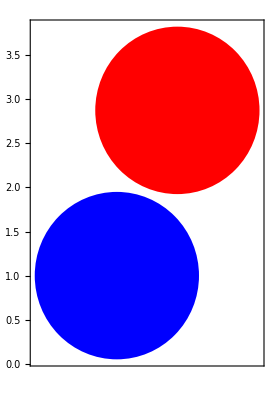

```mathematica
beeswarmPlot[dddd,Blend[{{Min[dddd],Blue},{Max[dddd],Red}},#]&/@dddd,
1,AspectRatio->Automatic]
```

## Make plots

```mathematica
(*data come from hepatocellular-carcinoma-data.ipynb*)
```

```mathematica
dataDir="~/ASUDropbox/Research/bees/geneExpression/Code/";dataEarly=Transpose[Import[dataDir<>"230407_HCC_reduced_data_early.HCC.csv","Data"][[2;;]]];
dataAdvanced=Transpose[Import[dataDir<>"230407_HCC_reduced_data_advanced.HCC.csv","Data"][[2;;]]];
dataVeryAdvanced=Transpose[Import[dataDir<>"230407_HCC_reduced_data_very.advanced.HCC.csv","Data"][[2;;]]];
```

```mathematica
{Dimensions[dataEarly],Dimensions[dataAdvanced],Dimensions[dataVeryAdvanced]}
```

{{2,20},{2,17},{2,20}}

```mathematica
fitParamsEarly={{0,{c->-4.146006155104734,d->3.4284635998558386,nuMu->-4.161310150472927}}};
fitParamsAdvanced={{0,{c->-6.0086274271638995,d->4.68636640429777,nuMu->-20.865903873712483}}};
fitParamsVeryAdvanced={{0,{c->-6.771279013425548,d->5.731380005674793,nuMu->-6.87441496045189}}};
```

```mathematica
fitValsEarly={0.0002787976803662886};
fitValsAdvanced={0.0002044063176119739};
fitValsVeryAdvanced={0.0001427442190429949};
```

```mathematica
(*control cases are plotted in purple, everything else in orange*)
```

```mathematica
SeedRandom[1234];{
bistablePlotEigvec[dataEarly,{0.},fitValsEarly,{{1.}},fitParamsEarly,1,"HCC_early"],
bistablePlotEigvec[dataAdvanced,{0.},fitValsAdvanced,{{1.}},fitParamsAdvanced,1,"HCC_advanced"],
bistablePlotEigvec[dataVeryAdvanced,{0.},fitValsVeryAdvanced,{{1.}},fitParamsVeryAdvanced,1,"HCC_very_advanced"]
}
```

{~/Dropbox (ASU)/Research/bees/geneExpression/Plots/230407_bistable_plot_along_eigvec_HCC_early_nuIndex1.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/230407_bistable_plot_along_eigvec_HCC_advanced_nuIndex1.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/230407_bistable_plot_along_eigvec_HCC_very_advanced_nuIndex1.pdf}